```mathematica
Exit[]
```

```mathematica
Needs["PM`"]
UninstallPackages[$PM,{"KnotToolsLink"}];
ClearAllCache[$PM];
LoadPackages[{"Geometries","KnotToolsLink"}]
```

Deleting package KnotToolsLink.

Deleting installation path.

Deleting files {/Users/jasoncantarella/Dropbox/Jason/PackageSources_2024-10-17T14:29:03/PackageSources/KnotToolsLink/PlanarDiagramObject_Library.nb}

WARNING: LTemplate has not yet been tested with Mathematica 14.1.0.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

Updating package KnotToolsLink...

/Users/jasoncantarella/Dropbox/Jason/PackageSources_2024-10-17T14:29:03/PackageSources/KnotToolsLink/LibrarySources/PlanarDiagramObject/

Exporting library PlanarDiagramObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source.

Names of functions in library PlanarDiagramObject are made public.

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source

Unloading library PlanarDiagramObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 14.3101

```mathematica
(*Exit[]*)
```

```mathematica
(*Most of the time you do not have to recompile. Then load the package like this is faster.*)
Needs["PM`"]
LoadPackages[{"Geometries","KnotToolsLink"}]
```

```mathematica
hardknotfiles=FileNames[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","diagrams","hardunknots","*.tsv"}]];
```

```mathematica
PD=PlanarDiagram[Import[Echo[hardknotfiles[[14]]]],0]
```

/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/OchaiIV.tsv

PlanarDiagramObject[…]

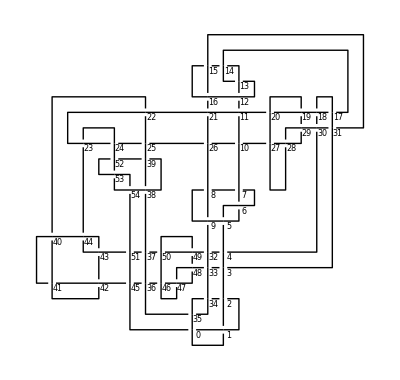

```mathematica
PlotDiagram[PD]
```

```mathematica
PD1=SimplifyDiagram4[PD]
```

PlanarDiagramObject[…]

```mathematica
ReginaHOMFLY[PDCode[PD]][L,M]
```

ReginaHOMFLY: time elapsed→0.05834

1

```mathematica
PDSnaPy=SnapPySymplifyPickup[PDCode[PD]]
```

0.377525 s elapsed while compiling PDCodeAppendSign.

Writing to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/MacOSX-ARM64/PDCodeAppendSign.dylib.

<|PDCode→{{8,14,9,13,1},{14,10,15,9,1},{10,16,11,15,1},{93,16,94,17,-1},{98,18,99,17,1},{18,24,19,23,1},{24,20,25,19,1},{20,26,21,25,1},{21,62,22,63,-1},{63,22,64,23,-1},{47,26,48,27,-1},{27,40,28,41,-1},{28,34,29,33,1},{34,30,35,29,1},{30,36,31,35,1},{31,58,32,59,-1},{59,32,60,33,-1},{36,96,37,95,1},{96,38,97,37,1},{51,38,52,39,-1},{39,52,40,53,-1},{60,42,61,41,1},{73,42,74,43,-1},{106,44,107,43,1},{44,108,45,107,1},{45,72,46,73,-1},{46,62,47,61,1},{48,54,49,53,1},{54,50,55,49,1},{50,56,51,55,1},{97,56,98,57,-1},{57,94,58,95,-1},{99,64,100,65,-1},{92,66,93,65,1},{11,66,12,67,-1},{67,12,68,13,-1},{83,68,84,69,-1},{102,70,103,69,1},{70,2,71,1,1},{2,72,3,71,1},{74,80,75,79,1},{80,76,81,75,1},{76,82,77,81,1},{77,104,78,105,-1},{105,78,106,79,-1},{82,8,83,7,1},{84,90,85,89,1},{90,86,91,85,1},{86,92,87,91,1},{87,100,88,101,-1},{101,88,102,89,-1},{103,6,104,7,-1},{3,108,4,109,-1},{109,4,0,5,-1},{5,0,6,1,-1}},Timing→0.011402,Method→SnapPySymplifyPickup|>

```mathematica
PDRegina=ReginaSimplify[PDCode[PD]]
```

<|PDCode→{{0,106,1,105,1},{4,10,5,9,1},{6,12,7,11,1},{7,48,8,49,-1},{10,6,11,5,1},{13,26,14,27,-1},{14,20,15,19,1},{16,22,17,21,1},{17,44,18,45,-1},{20,16,21,15,1},{22,82,23,81,1},{25,38,26,39,-1},{30,94,31,93,1},{31,58,32,59,-1},{32,48,33,47,1},{33,12,34,13,-1},{34,40,35,39,1},{36,42,37,41,1},{37,24,38,25,-1},{40,36,41,35,1},{43,80,44,81,-1},{45,18,46,19,-1},{46,28,47,27,1},{49,8,50,9,-1},{53,108,54,109,-1},{56,98,57,97,1},{59,28,60,29,-1},{60,66,61,65,1},{62,68,63,67,1},{63,90,64,91,-1},{66,62,67,61,1},{68,104,69,103,1},{69,54,70,55,-1},{70,76,71,75,1},{72,78,73,77,1},{73,86,74,87,-1},{76,72,77,71,1},{78,52,79,51,1},{79,2,80,3,-1},{82,24,83,23,1},{83,42,84,43,-1},{84,4,85,3,1},{85,50,86,51,-1},{87,74,88,75,-1},{88,56,89,55,1},{89,102,90,103,-1},{91,64,92,65,-1},{92,30,93,29,1},{95,100,96,101,-1},{98,58,99,57,1},{99,94,100,95,-1},{101,96,102,97,-1},{104,0,105,109,1},{106,2,107,1,1},{107,52,108,53,-1}},Timing→0.002095,Method→ReginaSimplify|>

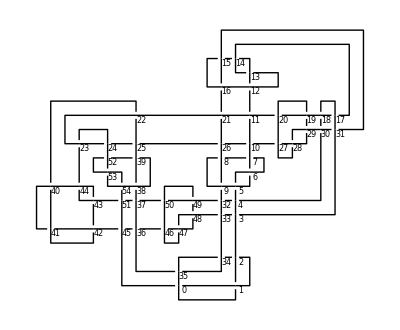

```mathematica
PlotDiagram[PD]
```

We’re going to assign a variable to each edge, giving the height of the edge as it leaves the crossing. We assume that edges stay at the same height through a crossing, so each arcline is going to need to access two heights; one as it leaves a crossing and the next arc in line’s height as it leaves the subsequent crossing. The quadratic objective function is just going to be the graph Laplacian of the cycle graph with 2n edges.  For each {a, b, c, d} in the PD code, we know that a is the incoming lower edge, c is the outgoing lower edge, and b and d are the overstrand, so we start by identifying these:

```mathematica
OutStrands[{a_,b_,c_,d_}]:= <|"under"->c,"over"->If[(b-d)^2==1,Max[{b,d}],Min[{b,d}]]|>;
```

Now we can set up a line in the constraint matrix so that when we dot it by vector of heights, the height associated with the overstrand is larger. We note that these matrix indices are offset by 1 from the edges they represent.

```mathematica
ConstraintLine[x_,r_]:={{r[[1]],#["under"]+1}->-1,{r[[1]],#["over"]+1}->+1}&@OutStrands[x[[1;;4]]] ;
```

```mathematica
BuildConstraintMatrix[PD_] := 
SparseArray[Flatten[
MapIndexed[
ConstraintLine,PD],
1],
{Length[PD],2Length[PD]}];
```

```mathematica
BuildConstraintMatrix[PDCode[PD]]
```

SparseArray[…]

```mathematica
BuildObjectiveFunction[PD_] :=(#.#)&@KirchhoffMatrix[CycleGraph[2*Length[PD]]]
```

```mathematica
BuildObjectiveFunction[PDCode[PD]]
```

SparseArray[…]

```mathematica
Timing[SuggestedLevels = QuadraticOptimization[BuildObjectiveFunction[PDCode@PD],{BuildConstraintMatrix[PDCode@PD],ConstantArray[-2,Length[PDCode@PD]]}];]
```

{0.054112,Null}

We now check that we’ve correctly encoded the constraints by checking that at each crossing the difference between the outgoing arcs obeys the condition:

```mathematica
LevelsFunctionOkQ[PD_,f_]:= And @@(f[[#["over"]+1]]-f[[#["under"]+1]] >= 2 & /@ (OutStrands /@ PD[[All,1;;4]]))
```

```mathematica
LevelsFunctionOkQ[PDCode[PD],SuggestedLevels]
```

True

So far, so good.

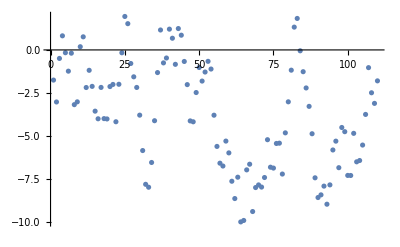

```mathematica
ListPlot[SuggestedLevels]
```

Here’s an experiment: what if we standardized the data by sort order to avoid different points being too close to each other.

```mathematica
DiscreteLevels = 2*Flatten[Values@ KeySort@PositionIndex[Sort[MapIndexed[{#1,#2[[1]]}&,SuggestedLevels]][[All,2]]],1];
```

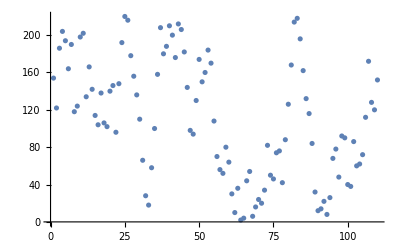

```mathematica
ListPlot[DiscreteLevels]
```

Now we need to construct new geometry according to the Levels embedding. We’ll need the ArcLines associated to the diagram. The strategy is to add a vertical segment to the curve at the first corner (or failing that, in the middle of the arc) which connects the levels at the start and end of the arc. So ArcLine[i] should be the line corresponding to edge i in the PD code (assuming that we’ve run CompressDiagramInPlace recently):

The value L[[i+1]] is the height of edge i at it’s outgoing crossing. L[[i+2]] is the height at the incoming crossing. We’ll make a new association which assigns this pair to each edge index.

```mathematica
ProcessArcLine[a_] := If[Length[a]==2,
{a[[1]],Mean[a],Mean[a],a[[2]]},
Join[a[[1;;2]],a[[2;;]]]]
```

```mathematica
LevelsEmbedding[PD_,L_]:= Block[{augmentedArcLines,al,procL,Lm=2,almost,edgeHeights},
edgeHeights = Association@MapIndexed[First[#2]-1->#1&,Transpose[{L,RotateLeft[L]}]];
al =  ProcessArcLine /@(Round[#,10]&/@ArcLines@Spherogram@PD);
Append[#,First[#]]&@DeleteDuplicates@Flatten[Table[
Join[
Append[edgeHeights[i][[1]]]/@al[i][[1;;2]],Append[edgeHeights[i][[2]]]/@al[i][[3;;]]
],{i,0,Length[L]-1} 
],1]
]
```

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,10*SuggestedLevels],1.0],ViewPoint->Top,ViewProjection->"Orthographic",ViewVertical->{0, 0, 1}]
```

-Graphics3D-

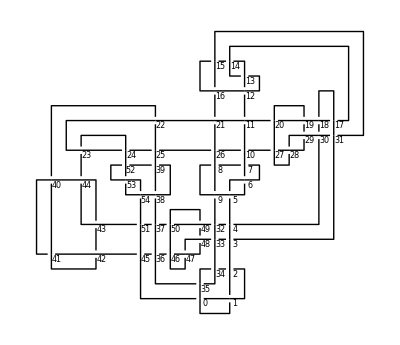

```mathematica
PlotDiagram[PD]
```

Now we need to rotate this to get some new perspectives on everything. If we just choose left or right we’ll have a lot of edges disappear. So we need to rotate to a “generic” view. First, we try something that’s very close to the z-projection.

```mathematica
A ={{1.,0.,0.},{0.,1.,0.},{0.134,0.2987,1}};
```

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,10*SuggestedLevels].A,1.0],ViewPoint->Top,ViewProjection->"Orthographic",ViewVertical->{0, 0, 1}]
```

-Graphics3D-

```mathematica
CheckPD = PlanarDiagram[10.0*LevelsEmbedding[PD,SuggestedLevels].A]
```

PlanarDiagramObject[…]

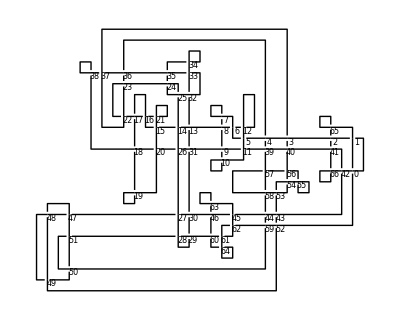

```mathematica
PlotDiagram[CheckPD]
```

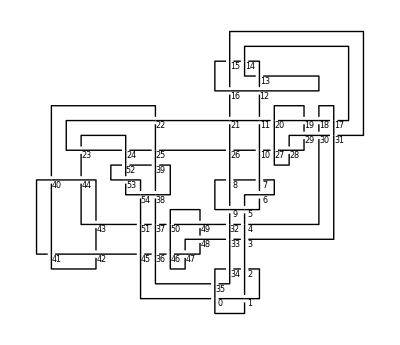

```mathematica
PlotDiagram[SimplifyDiagram4[CheckPD]]
```

```mathematica
CompressDiagramInPlace[CheckPD]
```

```mathematica
ReginaHOMFLY[PDCode[CheckPD]]
```

ReginaHOMFLY: time elapsed→0.05475

Function[{x,y},1]

```mathematica
R = RandomVariate[CircularRealMatrixDistribution[3]]
```

{{-0.0971777,0.740287,-0.66523},{-0.682185,0.43714,0.586116},{0.724693,0.510768,0.462533}}

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,10.0*SuggestedLevels].R,1],ViewPoint->Above]
```

-Graphics3D-

```mathematica
NewPD = PlanarDiagram[LevelsEmbedding[PD,10*SuggestedLevels].R]
```

PlanarDiagramObject[…]

```mathematica
(*Should be obsolete.*)
CompressDiagramInPlace[NewPD]
```

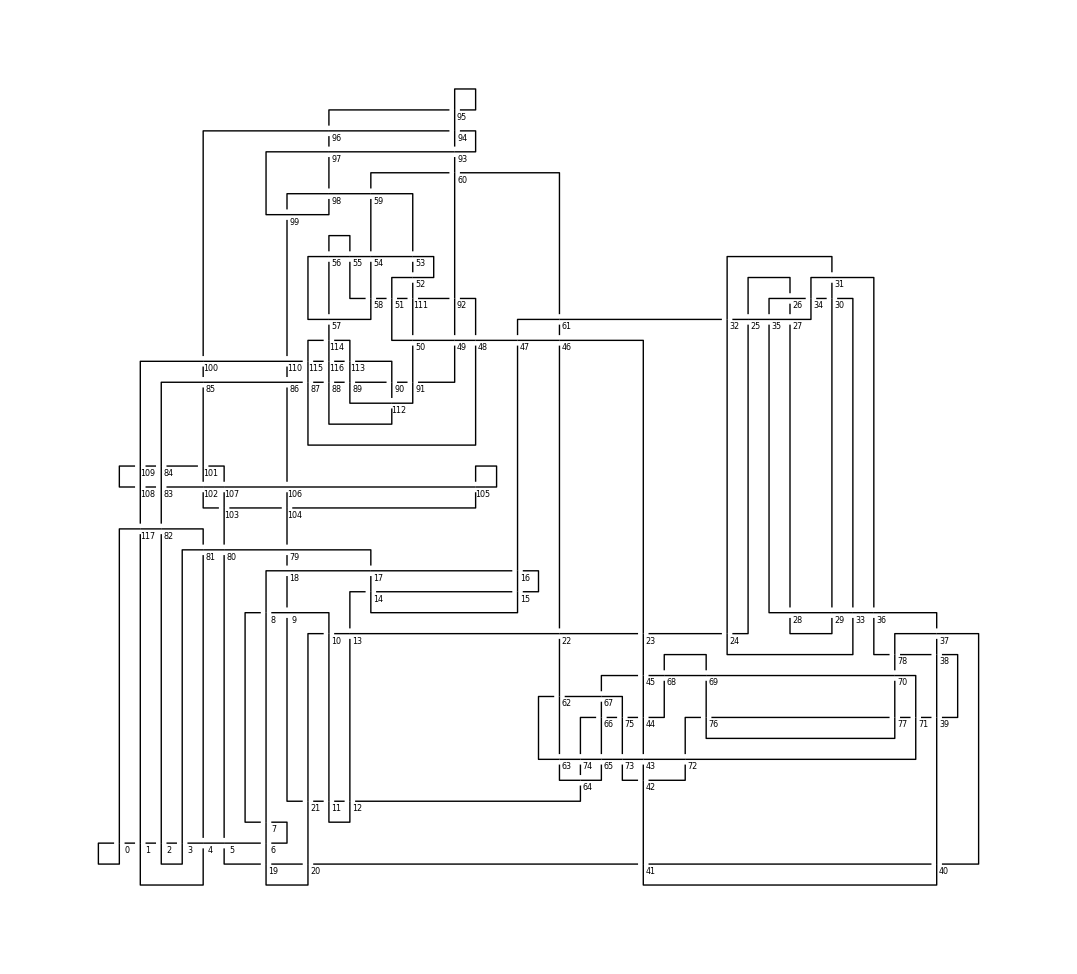

```mathematica
PlotDiagram[NewPD]
```

```mathematica
ReginaHOMFLY[PDCode[NewPD]]
```

ReginaHOMFLY: time elapsed→0.073142

Function[{x,y},1]

```mathematica
NewPDSimplified = SimplifyDiagram4[NewPD]
```

PlanarDiagramObject[…]